```mathematica
(*Import κ=0.1 and find eigen*)
κ=0.1;
g=1.5;
Get["/Users/zoe/Documents/Wolfram Mathematica/fig1_phiss_g1p5_k0p1"];
Phi0p1=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss0p1[x_]:=Phi0p1[(π^(1/2)*Exp[(2  π*κ)^(1/2)  x])/(1+Exp[(2  π*κ)^(1/2)  x])];
data=Table[{x,ϕss0p1[x]},{x,-50,50,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x]+g^2;
L=100;
dx=.05;
total=100;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->7000,"BasisSize"->total+1,"Shift"->2.8}];
```

InterpolatingFunction::dmval: Input value {1.08658×10^-17} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.08745×10^-17} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.08831×10^-17} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix … in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
(*find the k2b mode*)
2*Sqrt[vals[[1]]]
Sqrt[vals[[88]]]
```

3.24348

3.24194

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.782804}. NIntegrate obtained 0.00590027 and 1.61524×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.392179}. NIntegrate obtained 0.0000218464-0.0310332 ⅈ and 4.96835×10^-7 for the integral and error estimates.

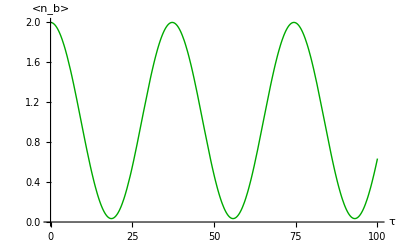

```mathematica
k=88;(*Put whatever k corresponds to the k2b mode,even*)
λ3=2*Pi^(3/2);
λ4=4*Pi*Pi/3;
Vbbbb=NIntegrate[cosTerm[x]*fns[[1]]^4,{x,-L/2,L/2}];
ωb=Sqrt[vals[[1]]];
k2b=Sqrt[(2*ωb)^2-g^2-2*Pi*κ];
fk[x_]:=(fns[[k+1]]+I*fns[[k]])/Sqrt[2]; (*Switch from even/odd to right/left moving*)
Vbbk=NIntegrate[Sin[intermediatePhi[x]]*fns[[1]]*fns[[1]]*fk[x],{x,-L/2,L/2}];
Bparam=λ3^2*Abs[Vbbk]^2/(4*ωb^3);
Cparam=3*I*λ4*Vbbbb/(4*ωb^2);
tMax=100; (*what time τ to evolve to*)
(*nb[t]=<n_b>,s[t]=<Σ^\dagger a_b a_b>,q[t]=<a_b^\dagger n_b a_b>,p[t]=<Σ^\dagger Σ>, IC is 2 excitations in bound state, 0 excitations in any of the scattering states*)
sol1=NDSolve[{nb'[t]==-2*Bparam*Re[s[t]],s'[t]==q[t]-Bparam*p[t]+Cparam*s[t],q'[t]==-2*Bparam*Re[s[t]],p'[t]==2*Re[s[t]],nb[0]==2,s[0]==0+0*I,q[0]==2,p[0]==0},{nb,s,q,p},{t,0,tMax}];
(*plot expectation value of number of occupations in bound state*)
Plot[nb[t]/. sol1,{t,0,tMax},AxesLabel->{Style["τ",14],Style["<n_b>",14]},PlotStyle->Directive[Darker@Green,Thick]]
```

```mathematica
(*Import κ=0.2 and find eigen*)
κ=0.2;
g=1.5;
Get["/Users/zoe/Documents/Wolfram Mathematica/fig1_phiss_g1p5_k0p2"];
Phi0p2=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss0p2[x_]:=Phi0p2[(π^(1/2)*Exp[(2  π*κ)^(1/2)  x])/(1+Exp[(2  π*κ)^(1/2)  x])];
data=Table[{x,ϕss0p2[x]},{x,-50,50,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x]+g^2;
L=100;
dx=.05;
total=90;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->7000,"BasisSize"->total+1,"Shift"->2.8}];
```

InterpolatingFunction::dmval: Input value {8.06134×10^-25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.07038×10^-25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.07944×10^-25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix … in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
(*find the k2b mode*)
2*Sqrt[vals[[1]]]
Sqrt[vals[[88]]]
```

3.35569

3.33609

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.584383}. NIntegrate obtained -0.0654836 and 1.79342×10^-7 for the integral and error estimates.

-0.0654836

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.392179}. NIntegrate obtained -0.0000201791+0.040324 ⅈ and 5.45619×10^-7 for the integral and error estimates.

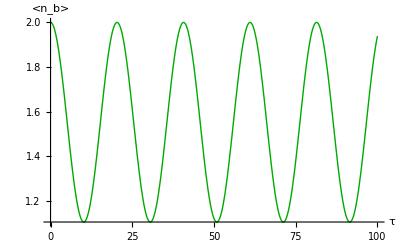

```mathematica
k=88;(*Put whatever k corresponds to the k2b mode,even*)
λ3=2*Pi^(3/2);
λ4=4*Pi*Pi/3;
Vbbbb=NIntegrate[cosTerm[x]*fns[[1]]^4,{x,-L/2,L/2}]
ωb=Sqrt[vals[[1]]];
k2b=Sqrt[(2*ωb)^2-g^2-2*Pi*κ];
fk[x_]:=(fns[[k+1]]+I*fns[[k]])/Sqrt[2]; (*Switch from even/odd to right/left moving*)
Vbbk=NIntegrate[Sin[intermediatePhi[x]]*fns[[1]]*fns[[1]]*fk[x],{x,-L/2,L/2}];
Bparam=λ3^2*Abs[Vbbk]^2/(4*ωb^3);
Cparam=3*I*λ4*Vbbbb/(4*ωb^2);
tMax=100; (*what time τ to evolve to*)
(*nb[t]=<n_b>,s[t]=<Σ^\dagger a_b a_b>,q[t]=<a_b^\dagger n_b a_b>,p[t]=<Σ^\dagger Σ>, IC is 2 excitations in bound state, 0 excitations in any of the scattering states*)
sol2=NDSolve[{nb'[t]==-2*Bparam*Re[s[t]],s'[t]==q[t]-Bparam*p[t]+Cparam*s[t],q'[t]==-2*Bparam*Re[s[t]],p'[t]==2*Re[s[t]],nb[0]==2,s[0]==0+0*I,q[0]==2,p[0]==0},{nb,s,q,p},{t,0,tMax}];
(*plot expectation value of number of occupations in bound state*)
Plot[nb[t]/. sol2,{t,0,tMax},AxesLabel->{Style["τ",14],Style["<n_b>",14]},PlotStyle->Directive[Darker@Green,Thick]]
```

```mathematica
(*Import κ=0.1 and find eigen*)
κ=0.3;
g=1.5;
Get["/Users/zoe/Documents/Wolfram Mathematica/fig1_phiss_g1p5_k0p3"];
Phi0p3=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss0p3[x_]:=Phi0p3[(π^(1/2)*Exp[(2  π*κ)^(1/2)  x])/(1+Exp[(2  π*κ)^(1/2)  x])];
data=Table[{x,ϕss0p3[x]},{x,-50,50,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x]+g^2;
L=100;
dx=.05;
total=100;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->7000,"BasisSize"->total+1,"Shift"->2.8}];
```

InterpolatingFunction::dmval: Input value {2.72665×10^-30} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.7304×10^-30} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.73415×10^-30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix … in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
(*find the k2b mode*)
2*Sqrt[vals[[1]]]
Sqrt[vals[[88]]]
```

3.42456

3.42787

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.193758}. NIntegrate obtained -0.127267 and 7.51162×10^-7 for the integral and error estimates.

-0.127267

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.392179}. NIntegrate obtained -0.0000180596+0.0440729 ⅈ and 5.78208×10^-7 for the integral and error estimates.

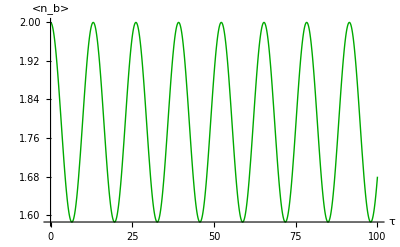

```mathematica
k=88;(*Put whatever k corresponds to the k2b mode,even*)
λ3=2*Pi^(3/2);
λ4=4*Pi*Pi/3;
Vbbbb=NIntegrate[cosTerm[x]*fns[[1]]^4,{x,-L/2,L/2}]
ωb=Sqrt[vals[[1]]];
k2b=Sqrt[(2*ωb)^2-g^2-2*Pi*κ];
fk[x_]:=(fns[[k+1]]+I*fns[[k]])/Sqrt[2]; (*Switch from even/odd to right/left moving*)
Vbbk=NIntegrate[Sin[intermediatePhi[x]]*fns[[1]]*fns[[1]]*fk[x],{x,-L/2,L/2}];
Bparam=λ3^2*Abs[Vbbk]^2/(4*ωb^3);
Cparam=3*I*λ4*Vbbbb/(4*ωb^2);
tMax=100; (*what time τ to evolve to*)
(*nb[t]=<n_b>,s[t]=<Σ^\dagger a_b a_b>,q[t]=<a_b^\dagger n_b a_b>,p[t]=<Σ^\dagger Σ>, IC is 2 excitations in bound state, 0 excitations in any of the scattering states*)
sol3=NDSolve[{nb'[t]==-2*Bparam*Re[s[t]],s'[t]==q[t]-Bparam*p[t]+Cparam*s[t],q'[t]==-2*Bparam*Re[s[t]],p'[t]==2*Re[s[t]],nb[0]==2,s[0]==0+0*I,q[0]==2,p[0]==0},{nb,s,q,p},{t,0,tMax}];
(*plot expectation value of number of occupations in bound state*)
Plot[nb[t]/. sol3,{t,0,tMax},AxesLabel->{Style["τ",14],Style["<n_b>",14]},PlotStyle->Directive[Darker@Green,Thick]]
```

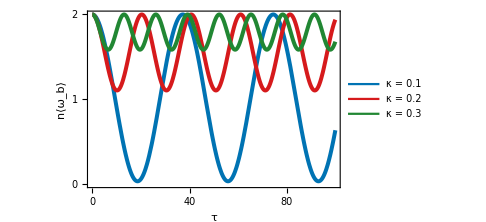

```mathematica
(*fancy plot*)
c1=RGBColor[0.00,0.45,0.70];
c2=RGBColor[0.84,0.10,0.11];
c3=RGBColor[0.13,0.53,0.20];

rabi=Plot[{nb[t]/. sol1,nb[t]/. sol2,nb[t]/. sol3},{t,0,tMax},PlotStyle->{{c1,Thickness[0.008]},{c2,Thickness[0.008]},{c3,Thickness[0.008]}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameTicks->{{{{0,"0"},{1,"1"},{2,"2"},{6,"6"},{8,"8"}},(*adjust to your y range*)None},{{{0,"0"},{20,"20"},{40,"40"},{60,"60"},{80,"80"},{100,"100"}},(*adjust to your y range*)None}},FrameTicksStyle->Directive[Black,12],FrameLabel->{Style["τ",Italic,14],Style["n⟨\!\(\*SubscriptBox[\(ω\), \(b\)]\)⟩",14]},PlotLegends->Placed[LineLegend[{c1,c2,c3},{Style["κ = 0.1",12],Style["κ = 0.2",12],Style["κ = 0.3",12]},LegendLayout->"Column"],After],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},ImageSize->5*72,ImagePadding->{{55,15},{40,15}},Background->White]
```

```mathematica
(*Export["/Users/zoe/Documents/AtomPaperFigures/rabi_original.pdf",rabi,ImageResolution->600]*)
```